```mathematica
s6=NDSolve[{D[A[x,y],{x,2}]+D[A[x,y],{y,2}]+56 A[x,y]==0,D[B[x,y],{x,2}]+D[B[x,y],{y,2}]+56 B[x,y]==0,A[0,y]==-1,A[2,y]==1,A[x,0]==0,A[x,1]==0,B[0,y]==0,B[2,y]==0,B[x,0]==-1,B[x,1]==1},{A[x,y],B[x,y]},{x,0,2},{y,0,1}]
```

{{A[x,y]→InterpolatingFunction[{{0., 2.}, {0., 1.}}, <>][x,y],B[x,y]→InterpolatingFunction[{{0., 2.}, {0., 1.}}, <>][x,y]}}

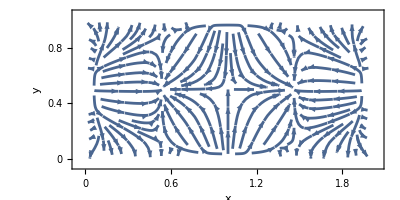

```mathematica
StreamPlot[Evaluate[{A[x,y],B[x,y]}/.s6],{x,0,2},{y,0,1},AspectRatio->1/2,StreamStyle->{Arrowheads[0.02],Thickness[0.005]},Frame->{True, True, True, True},PlotRange->{{-0.05,2.05},{-0.05,1.05}},FrameTicks->{{{0,0.2, 0.4, 0.6, 0.8,1},None},{{0,0.2, 0.4, 0.6, 0.8,1,1.2,1.4,1.6,1.8,2},None}},FrameLabel->{{"y", None},{"x", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36]]
```